Define the Recamán sequence:

```mathematica
Recaman[0]=0;
Recaman[1]=1;
Recaman[n_]:=Recaman[n]=Recaman[n-1]-If[Not[MemberQ[Table[Recaman[i],{i,0,n-1}],Recaman[n-1]-n]]&&(Recaman[n-1]-n>0),n,-n]
```

Number of steps taken:

```mathematica
MaxGraph=100;
```

Defining the graph:

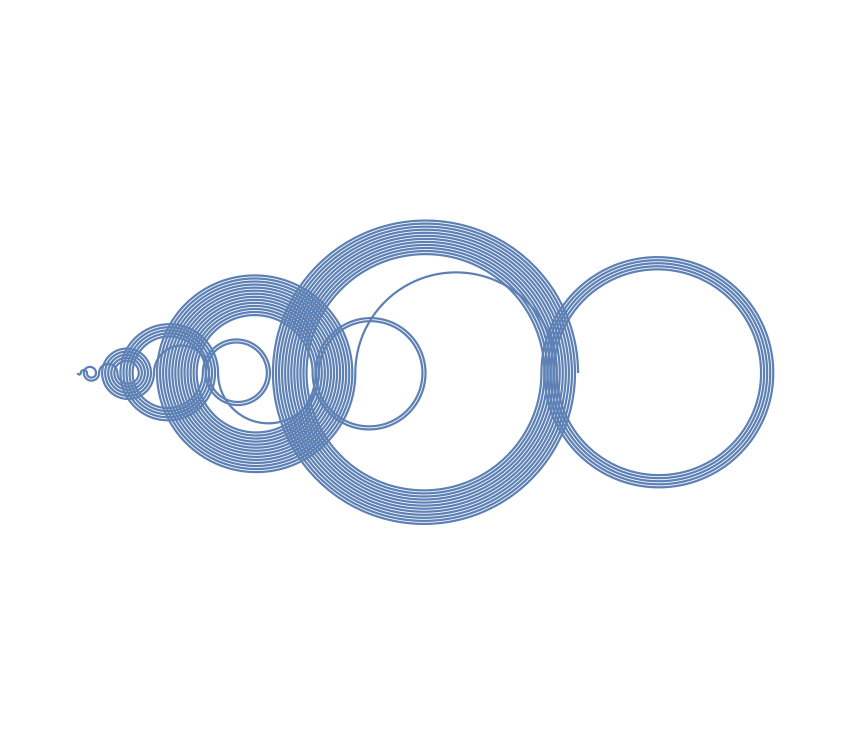

```mathematica
RecamanTable=Table[Recaman[n],{n,0,MaxGraph}];
Show[Table[ParametricPlot[Sign[1/2-Mod[n,2]]/2{Abs[(Recaman[n]-Recaman[n-1])]Cos[u],Sin[u]Abs[(Recaman[n]-Recaman[n-1])]}+{((Recaman[n]+Recaman[n-1])/2),0},{u,0,π},Axes->False,PlotRange->{{0,Max[RecamanTable]},{-MaxGraph,MaxGraph}}],{n,1,MaxGraph}]]
```

```mathematica
Manipulate[Table[Recaman[n],{n,0,counter}];
Show[Table[ParametricPlot[Sign[(-1)^n]/2{Abs[(Recaman[n]-Recaman[n-1])]Cos[u],Sin[u]Abs[(Recaman[n]-Recaman[n-1])]}+{((Recaman[n]+Recaman[n-1])/2),0},{u,0,π},Axes->False,PlotRange->{{0,150},{-40,40}}],{n,1,counter}]],{counter,1,100}]
```